```mathematica
<<Local`QFTToolKit`
QCDBaseIndices
Put[SaveFile=NBname["stub"]<>".out"];
```

{{0,1,2,3},{field,{1,2,3,4}},{feyn,{1,2,3,4,5}},{space,{1,2,3}},{timespace,{0,1}},{groupR,{1,2,3}},{gaugeG,{1,2,3,4,5,6,7,8}},{color,{1,2,3}},{flavor,{1,2,3,4,5,6}},{family,{1,2,3}}}

VI.8 Renormalization Groups

```mathematica
PR["Scattering amplitudes: ",e2=Subscript[ℳ, 2]->-I Subscript[λ, P][μ]+I C Subscript[λ, P][μ]^2(Log[(μ)^2/s]+Log[(μ)^2/t]+Log[(μ)^2/u]),and,e3=Subscript[ℳ, 3]->-I Subscript[λ, P][μ']+I C Subscript[λ, P][μ']^2(Log[(μ')^2/s]+Log[(μ')^2/t]+Log[(μ')^2/u]),
"Investigate behavior of λ_P near μ'⟶μ where we expect ℳ's to be equal.
Subtracting: ",tmp=SubtractRules[{e2,e3}],
Yield,tmp0=0->tmp[[2]],
Imply,tmp=tmp0//PowerExpand,
NL,"Represent ",sub=Subscript[λ, P][μ']^2->(Subscript[λ, P][μ]+δ)^2," where δ<<λ_P.",
Imply,tmp=tmp/.sub,
NL,"For ",sub=δ->0,
Yield,tmp=xRuleX[tmp,Subscript[λ, P][μ']]/.sub//Simplify//gatherLog//First,CG[" (4)"],
NL,"Differential Form: ",
tmp=D[#,μ']&/@tmp/.μ'->μ
]
```

Scattering amplitudes: ℳ_2→-ⅈ λ_P[μ]+ⅈ C (Log[μ^2/s]+Log[μ^2/t]+Log[μ^2/u]) λ_P[μ]^2 and ℳ_3→-ⅈ λ_P[μ']+ⅈ C (Log[(μ')^2/s]+Log[(μ')^2/t]+Log[(μ')^2/u]) λ_P[μ']^2Investigate behavior of λ_P near μ'⟶μ where we expect ℳ's to be equal.
Subtracting: ℳ_2-ℳ_3→-ⅈ λ_P[μ]+ⅈ C (Log[μ^2/s]+Log[μ^2/t]+Log[μ^2/u]) λ_P[μ]^2+ⅈ λ_P[μ']-ⅈ C (Log[(μ')^2/s]+Log[(μ')^2/t]+Log[(μ')^2/u]) λ_P[μ']^2
→ 0→-ⅈ λ_P[μ]+ⅈ C (Log[μ^2/s]+Log[μ^2/t]+Log[μ^2/u]) λ_P[μ]^2+ⅈ λ_P[μ']-ⅈ C (Log[(μ')^2/s]+Log[(μ')^2/t]+Log[(μ')^2/u]) λ_P[μ']^2
⇒ 0→-ⅈ λ_P[μ]+ⅈ C (-Log[s]-Log[t]-Log[u]+6 Log[μ]) λ_P[μ]^2+ⅈ λ_P[μ']-ⅈ C (-Log[s]-Log[t]-Log[u]+6 Log[μ']) λ_P[μ']^2
Represent λ_P[μ']^2→(δ+λ_P[μ])^2 where δ<<λ_P.
⇒ 0→-ⅈ λ_P[μ]+ⅈ C (-Log[s]-Log[t]-Log[u]+6 Log[μ]) λ_P[μ]^2-ⅈ C (-Log[s]-Log[t]-Log[u]+6 Log[μ']) (δ+λ_P[μ])^2+ⅈ λ_P[μ']
For δ→0
→ λ_P[μ']→λ_P[μ] (1+6 C Log[μ'/μ] λ_P[μ]) (4)
Differential Form: λ_P'[μ]→(6 C λ_P[μ]^2)/μ

```mathematica
PR["Important result: ",e15=T[λ',"d"][n_]->b^((n/2)(d-2)-d)T[λ,"d"][n],
" where ",sub=Λ-δ[Λ]->b Λ,
imply,subb=xRuleX[sub,b][[1]]//Simplify,
NL,"If ",sub=e15[[1]]->T[λ,"d"][n]+δ[T[λ,"d"][n]],
Imply,tmp=e15/.sub//RemovePatterns,
yield,tmp=tmp/.subb,
NL,"Expanding δ[Λ] keep first order in δ: ",
tmp=MapAt[Series[#,{δ[Λ],0,2}]&,tmp,2]//Normal;
yield,tmp=tmp/.δ[_]^2->0;
yield,tmpd=xRuleX[tmp,δ[T[λ,"d"][n]]]//Simplify//First,
NL,"Changing resolution: ",tmp=L->1/Λ,
yield,tmp=Log/@tmp,
yield,tmp=Dt/@tmp/.Dt->δ,
yield,tmp=xRuleX[tmp,δ[Λ]],
Imply,tmpd/.tmp//Map[L #/δ[L]&,#]&,CR[" Opposite sign from (16)"]
]
```

Important result: λ'_n_^n_→b^(-d+1/2 (-2+d) n) λ_n^n where Λ-δ[Λ]→b Λ ⇒ b→1-δ[Λ]/Λ
If λ'_n_^n_→λ_n^n+δ[λ_n^n]
⇒ λ_n^n+δ[λ_n^n]→b^(-d+1/2 (-2+d) n) λ_n^n ⟶ λ_n^n+δ[λ_n^n]→λ_n^n (1-δ[Λ]/Λ)^(-d+1/2 (-2+d) n)
Expanding δ[Λ] keep first order in δ:  ⟶  ⟶ δ[λ_n^n]→-((d (-2+n)-2 n) λ_n^n δ[Λ])/(2 Λ)
Changing resolution: L→1/Λ ⟶ Log[L]→Log[1/Λ] ⟶ δ[L]/L→-δ[Λ]/Λ ⟶ {δ[Λ]→-(Λ δ[L])/L}
⇒ (L δ[λ_n^n])/δ[L]→1/2 (d (-2+n)-2 n) λ_n^n Opposite sign from (16)

```mathematica
PR1[CO["V1.8.1: Show that the solution of ",tmp=xPartialD[g,t]->-b g^3," is given by ",
1/α[t]->1/α[0]+ 8 π b t," where we defined ",subα=α[t]->g[t]^2/(4 π)],
NL,"Notation change for Mathematica and solving: ",sub={g->g[t],xPartialD->D},
Imply,tmp=tmp/.sub,
yield,tmp=DSolve[tmp/.Rule->Equal,g,t];
yield,tmp=g[t]^2->(tmp[[2,1,2]][t])^2,
NL,"From the definition: ",
sub=xRuleX[subα,g[t]],
Imply,tmp=tmp/.sub,
imply,sub=xRuleX[tmp/.t->0,C[1]][[1]],
imply,tmp=tmp/.sub,
yield,tmp=4π/(#)&/@tmp//Simplify,CG["QED"]
];
```

V1.8.1: Show that the solution of UnderBar[∂]_t[g]→-b g^3 is given by 1/α[t]→8 b π t+1/α[0] where we defined α[t]→g[t]^2/(4 π)
Notation change for Mathematica and solving: {g→g[t],xPartialD→D}
⇒ g'[t]→-b g[t]^3 ⟶  ⟶ g[t]^2→1/(2 b t-2 C[1])
From the definition: {g[t]→-2 √π √α[t],g[t]→2 √π √α[t]}
⇒ 4 π α[t]→1/(2 b t-2 C[1]) ⇒ C[1]→-1/(8 π α[0]) ⇒ 4 π α[t]→1/(2 b t+1/(4 π α[0])) ⟶ 1/α[t]→8 b π t+1/α[0]QED

```mathematica
PR[CO["VI.8.2: In our discussion off the renormalization group, in ",λ ϕ^4," theory or in QED, for the sake of simplicity we assumed that the mass m of the particle is much smaller the μ and thus set m equal to zero.  But nothing in the renormalization group idea tells us that we can't flow to a mass scale below m.  Indeed, in particle physics many orders of magnitude separate the top quark mass m_t from the up quark mass m_u.  We might want to study how the strong interaction coupling flows from some mass scale far above m_t down to some mass scale μ equal to zero and any m above μ to infinity (i.e., not contributing to the renormalization group flow).  In reality, as μ approaches m from above the particle starts to contribute less and drops out as μ becomes much less than m.  Taking either the ",λ ϕ^4," theory or QED study this so-called threshold effect."]
]
```

VI.8.2: In our discussion off the renormalization group, in λ ϕ^4 theory or in QED, for the sake of simplicity we assumed that the mass m of the particle is much smaller the μ and thus set m equal to zero.  But nothing in the renormalization group idea tells us that we can't flow to a mass scale below m.  Indeed, in particle physics many orders of magnitude separate the top quark mass m_t from the up quark mass m_u.  We might want to study how the strong interaction coupling flows from some mass scale far above m_t down to some mass scale μ equal to zero and any m above μ to infinity (i.e., not contributing to the renormalization group flow).  In reality, as μ approaches m from above the particle starts to contribute less and drops out as μ becomes much less than m.  Taking either the λ ϕ^4 theory or QED study this so-called threshold effect.

VI.8.2:  λϕ^4theory

```mathematica
PR["● Working with λ^2 correction of λϕ^4 theory the scattering amplitude (III.1.1): ",
NL,$M=ℳ->HoldForm[(1/2)(-I λ)^2 I^2]IntegralOp[{{k}},1/(2π)^4 1/(k^2-m^2+I ε)1/((K-k)^2-m^2+I ε)],
NL,"where ",K->{s,t,u},
NL,"• Use the PS.6.42 to evaluate: ",
$d=PS642[2]/.{Subscript[m, 1|2]->1,Subscript[A, 1]->(k^2-m^2+I ε),Subscript[A, 2]->((K-k)^2-m^2+I ε)},
NL,"• Add indices to vectors quantities: ",
$dpos=ExtractPositionPattern[$d,1/(a_+b_)^2]/.{k^2->T[k,"u"][μ]T[k,"d"][μ],(K-k)^2->(T[K,"u"][μ]-T[k,"u"][μ])(T[K,"d"][μ]-T[k,"d"][μ])},
Yield,$d=ReplacePartTU[$d,$dpos],
NL,"• Do x_2 integral with δ-function: ",
NL,$d[[2]]=$d[[2]]/.separateIntegralOp//integrateδfuncRule1[{Subscript[x, 2],0,1}]//Refine[#,{Subscript[x, 1]∈Reals,0<Subscript[x, 1]<1}]&,
NL,"• Complete square on denominator term: ",
$pos=ExtractPositionPattern[$d,1/a_^2];
$dx=$pos[[1,2]]//Denominator//First,
NL," wrt: ",
$k=T[k,"d"][μ],
Yield,$dx=CompleteSquareUpDn[$dx,$k]/.T[K,"u"][μ]T[K,"u"][μ]->T[K,"u"][μ]T[K,"d"][μ]/.ϵ->ε,
Yield,$pos[[1,2]]=1/$dx[[1]]^2,
$d=ReplacePartTU[$d,$pos]/.ϵ->ε
]
```

● Working with λ^2 correction of λϕ^4 theory the scattering amplitude (III.1.1): 
ℳ→(1/2 (-ⅈ λ)^2 ⅈ^2) ∫_{k} [1/(16 π^4 (k^2-m^2+ⅈ ε) ((-k+K)^2-m^2+ⅈ ε))]
where K→{s,t,u}
• Use the PS.6.42 to evaluate: 1/((k^2-m^2+ⅈ ε) ((-k+K)^2-m^2+ⅈ ε))→∫_({x_1,0,1}
{x_2,0,1}) [(Γ[2] δ[-1+x_1+x_2])/(((k^2-m^2+ⅈ ε) x_1+((-k+K)^2-m^2+ⅈ ε) x_2)^2 Γ[1]^2)]
• Add indices to vectors quantities: {{2,2,1}→1/((x_1 (-m^2+ⅈ ε+k_μ^μ k_μ^μ)+x_2 (-m^2+ⅈ ε+(-k_μ^μ+K_μ^μ) (-k_μ^μ+K_μ^μ)))^2)}
→ 1/((k^2-m^2+ⅈ ε) ((-k+K)^2-m^2+ⅈ ε))→∫_({x_1,0,1}
{x_2,0,1}) [(Γ[2] δ[-1+x_1+x_2])/((x_1 (-m^2+ⅈ ε+k_μ^μ k_μ^μ)+x_2 (-m^2+ⅈ ε+(-k_μ^μ+K_μ^μ) (-k_μ^μ+K_μ^μ)))^2 Γ[1]^2)]
• Do x_2 integral with δ-function: 
∫_{x_1,0,1} [Γ[2]/((m^2-ⅈ ε+(-1+x_1) K_μ^μ (-k_μ^μ+K_μ^μ)-k_μ^μ (k_μ^μ+(-1+x_1) K_μ^μ))^2 Γ[1]^2)]
• Complete square on denominator term: m^2-ⅈ ε+(-1+x_1) K_μ^μ (-k_μ^μ+K_μ^μ)-k_μ^μ (k_μ^μ+(-1+x_1) K_μ^μ)
 wrt: k_μ^μ
→ {-(k_μ^μ+(-1+x_1) K_μ^μ) (k_μ^μ+(-1+x_1) K_μ^μ)+1/4 (4 (-1+x_1)^2 K_μ^μ K_μ^μ+4 (m^2-ⅈ ε+(-1+x_1) K_μ^μ K_μ^μ)),-1,(-1+x_1) K_μ^μ,1/4 (4 (-1+x_1)^2 K_μ^μ K_μ^μ+4 (m^2-ⅈ ε+(-1+x_1) K_μ^μ K_μ^μ))}
→ 1/((-(k_μ^μ+(-1+x_1) K_μ^μ) (k_μ^μ+(-1+x_1) K_μ^μ)+1/4 (4 (-1+x_1)^2 K_μ^μ K_μ^μ+4 (m^2-ⅈ ε+(-1+x_1) K_μ^μ K_μ^μ)))^2)1/((k^2-m^2+ⅈ ε) ((-k+K)^2-m^2+ⅈ ε))→∫_{x_1,0,1} [Γ[2]/((-(k_μ^μ+(-1+x_1) K_μ^μ) (k_μ^μ+(-1+x_1) K_μ^μ)+1/4 (4 (-1+x_1)^2 K_μ^μ K_μ^μ+4 (m^2-ⅈ ε+(-1+x_1) K_μ^μ K_μ^μ)))^2 Γ[1]^2)]

```mathematica
PR["● Scattering amplitude: ",$M1=$M/.$d/.IntegralOp->simpleIntegralOp/.IntegralOp[a_,IntegralOp[b_,c_]]->IntegralOp[b,IntegralOp[a,c]],
NL,"Do k-integral: ",$pos1=ExtractPositionPattern[$M1,IntegralOp[{{k}},_]],
NL,"Using the template: ",
$t=e1427hitoshi,
NL,"and Applying: ",$s={a->0,b->2,q^2->($k+$dx[[3]])RaiseIndexTU[μ,μ][($k+$dx[[3]])],D->$dx[[-1]]},
NL,"The original integral is recovered: ",
Yield,$t=$t/.$s//Simplify,
NL,"0-order expansion of the RHS around d->4: ",
$t[[2]]=Series[$t[[2]],{d,4,0}]//Normal//Simplify;$t,
$pos1[[1,2]]=$t[[2]];$pos1;
$M1=ReplacePartTU[$M1,$pos1],
Yield,$M1=$M1/.IntegralOp->simpleIntegralOp/.subxIntegrate/.addAssumptions[{T[K,"u"][μ],T[K,"d"][μ],ε,m}∈Reals]/.subIntegrate
]
```

● Scattering amplitude: ℳ→((1/2 (-ⅈ λ)^2 ⅈ^2) ∫_{x_1,0,1} [∫_{k} [1/((-(k_μ^μ+(-1+x_1) K_μ^μ) (k_μ^μ+(-1+x_1) K_μ^μ)+1/4 (4 (-1+x_1)^2 K_μ^μ K_μ^μ+4 (m^2-ⅈ ε+(-1+x_1) K_μ^μ K_μ^μ)))^2)]] Γ[2])/(16 π^4 Γ[1]^2)
Do k-integral: {{2,4,2}→∫_{k} [1/((-(k_μ^μ+(-1+x_1) K_μ^μ) (k_μ^μ+(-1+x_1) K_μ^μ)+1/4 (4 (-1+x_1)^2 K_μ^μ K_μ^μ+4 (m^2-ⅈ ε+(-1+x_1) K_μ^μ K_μ^μ)))^2)]}
Using the template: ∫_{q} [(q^2)^a (-D+q^2-ⅈ ε)^-b]→(ⅈ (-1)^(a+b) D^(a-b+d/2) π^(d/2) Gamma[-a+b-d/2] Gamma[a+d/2])/(Gamma[b] Gamma[d/2])
and Applying: {a→0,b→2,q^2→(k_μ^μ+(-1+x_1) K_μ^μ) (k_μ^μ+(-1+x_1) K_μ^μ),D→1/4 (4 (-1+x_1)^2 K_μ^μ K_μ^μ+4 (m^2-ⅈ ε+(-1+x_1) K_μ^μ K_μ^μ))}
The original integral is recovered: 
→ ∫_{q} [1/((-m^2+(-1+x_1) k_μ^μ K_μ^μ+K_μ^μ K_μ^μ-x_1 K_μ^μ K_μ^μ+k_μ^μ (k_μ^μ+(-1+x_1) K_μ^μ))^2)]→ⅈ π^(d/2) Gamma[2-d/2] (m^2-ⅈ ε-x_1 K_μ^μ K_μ^μ+x_1^2 K_μ^μ K_μ^μ)^(-2+d/2)
0-order expansion of the RHS around d->4: ∫_{q} [1/((-m^2+(-1+x_1) k_μ^μ K_μ^μ+K_μ^μ K_μ^μ-x_1 K_μ^μ K_μ^μ+k_μ^μ (k_μ^μ+(-1+x_1) K_μ^μ))^2)]→-ⅈ π^2 (2/(-4+d)+EulerGamma+Log[π]+Log[m^2-ⅈ ε-x_1 K_μ^μ K_μ^μ+x_1^2 K_μ^μ K_μ^μ])ℳ→((1/2 (-ⅈ λ)^2 ⅈ^2) ∫_{x_1,0,1} [-ⅈ π^2 (2/(-4+d)+EulerGamma+Log[π]+Log[m^2-ⅈ ε-x_1 K_μ^μ K_μ^μ+x_1^2 K_μ^μ K_μ^μ])] Γ[2])/(16 π^4 Γ[1]^2)
→ ℳ→ConditionalExpression[-(ⅈ (1/2 (-ⅈ λ)^2 ⅈ^2) (2/(-4+d)+EulerGamma+Log[π]+(-2 (K_μ^μ)^(1/2) (K_μ^μ)^(1/2)+Log[m^2-ⅈ ε] (K_μ^μ)^(1/2) (K_μ^μ)^(1/2)+2 ArcTan[((K_μ^μ)^(1/2) (K_μ^μ)^(1/2))/(√(4 m^2-4 ⅈ ε-K_μ^μ K_μ^μ))] √(4 m^2-4 ⅈ ε-K_μ^μ K_μ^μ))/((K_μ^μ)^(1/2) (K_μ^μ)^(1/2))) Γ[2])/(16 π^2 Γ[1]^2),((√(K_μ^μ K_μ^μ (-4 m^2+K_μ^μ K_μ^μ)))/(K_μ^μ K_μ^μ)∉Reals||Re[(√(K_μ^μ K_μ^μ (-4 m^2+K_μ^μ K_μ^μ)))/(K_μ^μ K_μ^μ)]≥1||Re[(√(K_μ^μ K_μ^μ (-4 m^2+K_μ^μ K_μ^μ)))/(K_μ^μ K_μ^μ)]≤-1)&&((√(K_μ^μ K_μ^μ (-4 m^2+K_μ^μ K_μ^μ)))/(K_μ^μ K_μ^μ)∉Reals||Re[(√(K_μ^μ K_μ^μ (-4 m^2+K_μ^μ K_μ^μ)))/(K_μ^μ K_μ^μ)]<-1||Re[(√(K_μ^μ K_μ^μ (-4 m^2+K_μ^μ K_μ^μ)))/(K_μ^μ K_μ^μ)]>1)&&((√(K_μ^μ K_μ^μ (-4 m^2+4 ⅈ ε+K_μ^μ K_μ^μ)))/(K_μ^μ K_μ^μ)∉Reals||Re[(√(K_μ^μ K_μ^μ (-4 m^2+4 ⅈ ε+K_μ^μ K_μ^μ)))/(K_μ^μ K_μ^μ)]>1||Re[(√(K_μ^μ K_μ^μ (-4 m^2+4 ⅈ ε+K_μ^μ K_μ^μ)))/(K_μ^μ K_μ^μ)]<-1)&&(Re[(√(4 m^2-4 ⅈ ε-K_μ^μ K_μ^μ))/((K_μ^μ)^(1/2) (K_μ^μ)^(1/2))]≠0||Im[(√(4 m^2-4 ⅈ ε-K_μ^μ K_μ^μ))/((K_μ^μ)^(1/2) (K_μ^μ)^(1/2))]<-1||Im[(√(4 m^2-4 ⅈ ε-K_μ^μ K_μ^μ))/((K_μ^μ)^(1/2) (K_μ^μ)^(1/2))]>1)&&(Re[(√(K_μ^μ K_μ^μ (-4 m^2+4 ⅈ ε+K_μ^μ K_μ^μ)))/(K_μ^μ K_μ^μ)]==-1||Re[(√(K_μ^μ K_μ^μ (-4 m^2+4 ⅈ ε+K_μ^μ K_μ^μ)))/(K_μ^μ K_μ^μ)]==1||(√(K_μ^μ K_μ^μ (-4 m^2+4 ⅈ ε+K_μ^μ K_μ^μ)))/(K_μ^μ K_μ^μ)∉Reals||Re[(√(K_μ^μ K_μ^μ (-4 m^2+4 ⅈ ε+K_μ^μ K_μ^μ)))/(K_μ^μ K_μ^μ)]≤-1||Re[(√(K_μ^μ K_μ^μ (-4 m^2+4 ⅈ ε+K_μ^μ K_μ^μ)))/(K_μ^μ K_μ^μ)]≥1)]

```mathematica
PR["• The order-λ^2 amplitude with: ",$s=T[K,"d"][μ].T[K,"u"][μ]->stu," where stu is one of the Mandelstam variables.",
NL,$mx=$M1/.ε->0/.T[K,"u"][μ]->stu/T[K,"d"][μ]//FullSimplify;
$mx[[2,2]]=$mx[[2,2]]//PowerExpand;
$mx
]
PR["• The Sum this expression with (s->4m^2,t->0,u->0 channels) + constant ⟶ 0 ",
NL,"For ",$s=stu->4m^2,
Yield,$mxs=Limit[$mx[[2]],$s]//PowerExpand//FullSimplify,

NL,"For ",$s=stu->0,
Yield,$mxtu=Limit[$mx[[2]],$s]//PowerExpand//FullSimplify,
NL,"Sum of (s->4m^2,t->0,u->0 channels)->0 : ",
$mλ20=$mxs+2 $mxtu//FullSimplify
]
```

• The order-λ^2 amplitude with: K_μ^μ.K_μ^μ→stu where stu is one of the Mandelstam variables.
ℳ→ConditionalExpression[-(ⅈ (1/2 (-ⅈ λ)^2 ⅈ^2) (-2+2/(-4+d)+EulerGamma+(2 √(4 m^2-stu) ArcTan[(√stu)/(√(4 m^2-stu))])/(√stu)+Log[ⅈ m]+Log[-ⅈ m π]) Γ[2])/(16 π^2 Γ[1]^2),(Re[(√(-4 m^2+stu))/(√stu)]>1||1+Re[(√(-4 m^2+stu))/(√stu)]<0||(√(-4 m^2+stu))/(√stu)∉Reals)&&(Im[(√(4 m^2-stu))/(√stu)]>1||1+Im[(√(4 m^2-stu))/(√stu)]<0||Re[(√(4 m^2-stu))/(√stu)]≠0)]

• The Sum this expression with (s->4m^2,t->0,u->0 channels) + constant ⟶ 0 
For stu→4 m^2
→ -(ⅈ (1/2 (((-1)^2 ⅈ^2) λ^2) ⅈ^2) (10-4 EulerGamma+2 (-4+d) Log[m]-4 Log[π]+d (-2+EulerGamma+Log[π])) Γ[2])/(16 (-4+d) π^2 Γ[1]^2)
For stu→0
→ -(ⅈ (1/2 (((-1)^2 ⅈ^2) λ^2) ⅈ^2) (2+(-4+d) EulerGamma+2 (-4+d) Log[m]+(-4+d) Log[π]) Γ[2])/(16 (-4+d) π^2 Γ[1]^2)
Sum of (s->4m^2,t->0,u->0 channels)->0 : -(ⅈ (1/2 (((-1)^2 ⅈ^2) λ^2) ⅈ^2) (14-2 d-12 EulerGamma+3 d EulerGamma+6 (-4+d) Log[m]+3 (-4+d) Log[π]) Γ[2])/(16 (-4+d) π^2 Γ[1]^2)

```mathematica
PR["• Put it all together ",
Yield,$mall=($mx[[2]]/.stu->s)+($mx[[2]]/.stu->t)+($mx[[2]]/.stu->u)-$mλ20//FullSimplify//ReleaseHold,
NL,"Expand around d->4: ",
Yield,$mall=Subscript[ℳ, 2]->Series[$mall,{d,4,1}]/.Γ[a_]:>Gamma[a]//FullSimplify//gatherLog;Framed[$mall]
];
```

• Put it all together 
→ ConditionalExpression[1/(16 π^2 Γ[1]^2)ⅈ ((λ^2 (14-2 d-12 EulerGamma+3 d EulerGamma+6 (-4+d) Log[m]+3 (-4+d) Log[π]))/(2 (-4+d))+1/2 λ^2 (6-6/(-4+d)-3 EulerGamma-(2 √(4 m^2-s) ArcTan[(√s)/(√(4 m^2-s))])/(√s)-(2 √(4 m^2-t) ArcTan[(√t)/(√(4 m^2-t))])/(√t)-(2 √(4 m^2-u) ArcTan[(√u)/(√(4 m^2-u))])/(√u)-3 Log[ⅈ m]-3 Log[-ⅈ m π])) Γ[2],(Re[(√(-4 m^2+s))/(√s)]>1||1+Re[(√(-4 m^2+s))/(√s)]<0||(√(-4 m^2+s))/(√s)∉Reals)&&(Im[(√(4 m^2-s))/(√s)]>1||1+Im[(√(4 m^2-s))/(√s)]<0||Re[(√(4 m^2-s))/(√s)]≠0)&&(Re[(√(-4 m^2+t))/(√t)]>1||1+Re[(√(-4 m^2+t))/(√t)]<0||(√(-4 m^2+t))/(√t)∉Reals)&&(Im[(√(4 m^2-t))/(√t)]>1||1+Im[(√(4 m^2-t))/(√t)]<0||Re[(√(4 m^2-t))/(√t)]≠0)&&(Re[(√(-4 m^2+u))/(√u)]>1||1+Re[(√(-4 m^2+u))/(√u)]<0||(√(-4 m^2+u))/(√u)∉Reals)&&(Im[(√(4 m^2-u))/(√u)]>1||1+Im[(√(4 m^2-u))/(√u)]<0||Re[(√(4 m^2-u))/(√u)]≠0)]
Expand around d->4: 
→ ℳ_2→ConditionalExpression[(ⅈ λ^2 (4-(2 √(4 m^2-s) ArcTan[(√s)/(√(4 m^2-s))])/(√s)-(2 √(4 m^2-t) ArcTan[(√t)/(√(4 m^2-t))])/(√t)-(2 √(4 m^2-u) ArcTan[(√u)/(√(4 m^2-u))])/(√u)))/(32 π^2)+O[d-4]^2,(Re[(√(-4 m^2+s))/(√s)]>1||1+Re[(√(-4 m^2+s))/(√s)]<0||(√(-4 m^2+s))/(√s)∉Reals)&&(Im[(√(4 m^2-s))/(√s)]>1||1+Im[(√(4 m^2-s))/(√s)]<0||Re[(√(4 m^2-s))/(√s)]≠0)&&(Re[(√(-4 m^2+t))/(√t)]>1||1+Re[(√(-4 m^2+t))/(√t)]<0||(√(-4 m^2+t))/(√t)∉Reals)&&(Im[(√(4 m^2-t))/(√t)]>1||1+Im[(√(4 m^2-t))/(√t)]<0||Re[(√(4 m^2-t))/(√t)]≠0)&&(Re[(√(-4 m^2+u))/(√u)]>1||1+Re[(√(-4 m^2+u))/(√u)]<0||(√(-4 m^2+u))/(√u)∉Reals)&&(Im[(√(4 m^2-u))/(√u)]>1||1+Im[(√(4 m^2-u))/(√u)]<0||Re[(√(4 m^2-u))/(√u)]≠0)]

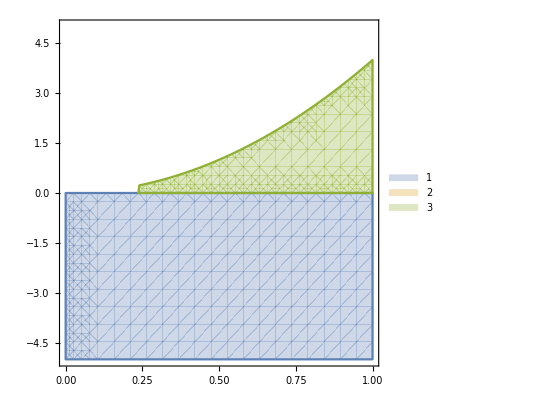
• RegionPlot of the Condition: RegionPlot[Re[(√(-4 m^2+s))/(√s)]>1||1+Re[(√(-4 m^2+s))/(√s)]<0||(√(-4 m^2+s))/(√s)∉Reals,{m,0,1},{s,-5,5},PlotLegends→Automatic]
-Graphics-
This shows that the only relavant condition applied here is 0<s<4 m^2

```mathematica
PR["• RegionPlot of the Condition: ",$1=HoldForm[RegionPlot][$mall[[2,2,1]],{m,0,1},{s,-5,5},PlotLegends->Automatic],
NL,ReleaseHold[$1/.Or->List],
NL,"This shows that the only relavant condition applied here is ",0<s<4 m^2
]
```

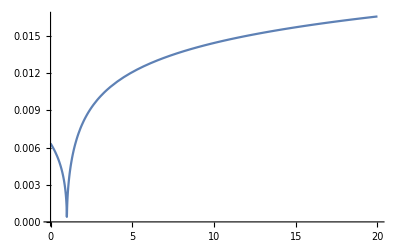
What about regions>4 m^2 ? Ignore Conditions.
Take: Limit[(ⅈ λ^2 (4-(2 √(4 m^2-s) ArcTan[(√s)/(√(4 m^2-s))])/(√s)-(2 √(4 m^2-t) ArcTan[(√t)/(√(4 m^2-t))])/(√t)-(2 √(4 m^2-u) ArcTan[(√u)/(√(4 m^2-u))])/(√u)))/(32 π^2)+O[d-4]^2,t→0]
And: Limit[(ⅈ λ^2 (1-(√(4 m^2-s) ArcTan[(√s)/(√(4 m^2-s))])/(√s)-(√(4 m^2-u) ArcTan[(√u)/(√(4 m^2-u))])/(√u)))/(16 π^2),u→0]
Remove coefficients: s→4 m^2 α
→ -(√(1-α) ArcTan[(√α)/(√(1-α))])/(16 π^2 √α)
Plot its Abs[]: -Graphics-
The function provides values outside the range of the ConditionExpression. Is this meaningful?

```mathematica
PR[CR["What about region",s>4m^2," ? Ignore Conditions."],
$=$mall[[2,1]];
NL,"Take: ",$=Inactive[Limit][$,t->0],$=Activate[$];
NL,"And: ",$=Inactive[Limit][$,u->0],$=Activate[$];
NL,"Remove coefficients: ",$s=s->α 4 m^2,
Yield,$=$/(I λ^2)/.$s//FullSimplify,
NL,"Plot its Abs[]: ",Plot[Abs[$],{α,0,20}],
NL,CR["The function provides values outside the range of the ConditionExpression. Is this meaningful?"]
];
```

VI.8.2: QED

```mathematica
PR["The QED renormalized propagator(4): ",
e4=I T[D^P,"dd"][μ,ν]->I T[D,"dd"][μ,ν]+I T[D,"dd"][μ,ν1]. I T[Π,"uu"][ν1,μ1]. I T[D,"dd"][μ1,ν]+zEtc[⋯],
Imply,e4a=e4[[1]]->-I (e^2/(q.q)).( 1/(1+e^2 Π[q^2])).(g@dd[μ,ν]-T[q,"d"][μ]T[q,"d"][ν]),
NL,"where the vacuum polarization correction III.7.12: ",
e12=T[Π,"dd"][μ,ν][q_]->1/(2 π^2)(T[q,"d"][μ]T[q,"d"][ν]-g@dd[μ,ν]q.q )IntegralOp[{{α,0,1}},Log[α(1-α)(m^2-α(1-α)q.q)]-xSum[Subscript[c, a] Log[α(1-α)(Subscript[m, a]^2-α(1-α)q.q)],{a}]],
NL,"Investigate the integral expression for varying values of m_a limiting to one mass scale {a}->{1}: ",
tmp=pos=ExtractPositionPattern[e12,IntegralOp[_,_]][[1]]/.xSum[a_,_]->a,
NL,"Integrating: ",
"POFF",
Yield,tmp=tmp[[2]]/.IntegralOp[b_,c_]->IntegralOp[{{α}},c],
Yield,tmp=tmp/.subxIntegrate,
Yield,tmp=tmp/.subIntegrate,
Yield,tmpa=Limit[tmp,α->0],
Yield,tmpb=Limit[tmp,α->1],
tmp=tmpb-tmpa//Simplify,
"PONdd",
NL,"Substituting ",sub={q.q->q2 Subscript[m, a]^2,Subscript[m, a]->m mam,Subscript[c, a]->1},
Imply,pos[[2]]=tmp//.sub//FullSimplify//PowerExpand,
Imply,tmpa=ReplacePartTU[e12,{pos}]
]
```

The QED renormalized propagator(4): ⅈ (D^P)_μν^μν→ⅈ D_μν^μν+ⅈ D_μν1^μν1.ⅈ Π_ν1μ1^ν1μ1.ⅈ D_μ1ν^μ1ν+zEtc[⋯]
⇒ ⅈ (D^P)_μν^μν→-ⅈ e^2/(q.q).1/(1+e^2 Π[q^2]).(g_μν^μν-q_μ^μ q_ν^ν)
where the vacuum polarization correction III.7.12: Π_μν^μν[q_]→(∫_{α,0,1} [Log[(1-α) α (m^2-(1-α) α q.q)]-UnderBar[∑]_{a}[Log[(1-α) α (-(1-α) α q.q+m_a^2)] c_a]] (-q.q g_μν^μν+q_μ^μ q_ν^ν))/(2 π^2)
Investigate the integral expression for varying values of m_a limiting to one mass scale {a}->{1}: {2,3}→∫_{α,0,1} [Log[(1-α) α (m^2-(1-α) α q.q)]-Log[(1-α) α (-(1-α) α q.q+m_a^2)] c_a]
Integrating: 
.......
Substituting {q.q→q2 m_a^2,m_a→m mam,c_a→1}
⇒ (-2 mam √(4-q2) ArcTan[(√q2)/(√(4-q2))]+2 √(4-mam^2 q2) ArcTan[(mam √q2)/(√(4-mam^2 q2))])/(mam √q2)-2 Log[mam]
⇒ Π_μν^μν[q_]→(((-2 mam √(4-q2) ArcTan[(√q2)/(√(4-q2))]+2 √(4-mam^2 q2) ArcTan[(mam √q2)/(√(4-mam^2 q2))])/(mam √q2)-2 Log[mam]) (-q.q g_μν^μν+q_μ^μ q_ν^ν))/(2 π^2)

Since(3): Π_μν^μν[q_]→-(q.q g_μν^μν-q_μ^μ q_ν^ν) Π[q^2]
⇒ Π[q^2]→(-mam √(4-q2) ArcTan[(√q2)/(√(4-q2))]+√(4-mam^2 q2) ArcTan[(mam √q2)/(√(4-mam^2 q2))]-mam √q2 Log[mam])/(mam π^2 √q2)
Examine: ⅈ (D^P)_μν^μν→-ⅈ e^2/(q.q).1/(1+e^2 Π[q^2]).(g_μν^μν-q_μ^μ q_ν^ν) ⇒ e_R^2→e^2/(1+e^2 Π[q^2])
For cases: {mam→0,mam→0.5,mam→1,mam→2,mam→4}

Case: mam→0 (m_a→0) ⇒  ⇒ e_R^2→0

Case: mam→0.5 (m_a→0.5 m) ⇒  ⇒ e_R^2→(14.2388 e^2 √q2)/((14.2388+1. e^2) √q2-1.4427 e^2 √(4.-1. q2) ArcTan[(√q2)/(√(4.-1. q2))]+2.88539 e^2 √(4.-0.25 q2) ArcTan[(0.5 √q2)/(√(4.-0.25 q2))])

Case: mam→1 (m_a→m) ⇒  ⇒ e_R^2→e^2

Case: mam→2 (m_a→2 m) ⇒  ⇒ e_R^2→(e^2 π^2 √q2)/(e^2 √(1-q2) ArcTan[(√q2)/(√(1-q2))]-e^2 √(4-q2) ArcTan[(√q2)/(√(4-q2))]+√q2 (π^2-e^2 Log[2]))

Case: mam→4 (m_a→4 m) ⇒  ⇒ e_R^2→(2 e^2 π^2 √q2)/(e^2 √(1-4 q2) ArcTan[(2 √q2)/(√(1-4 q2))]-2 e^2 √(4-q2) ArcTan[(√q2)/(√(4-q2))]+2 √q2 (π^2-e^2 Log[4]))

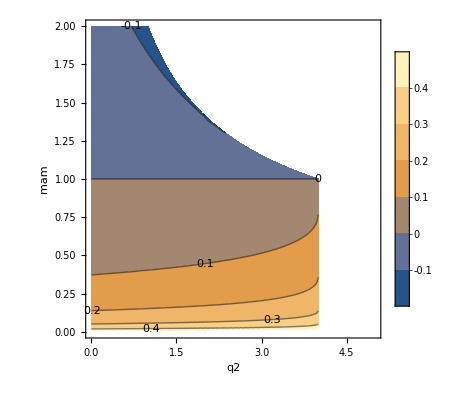
Plotting: Π[q^2]→(-mam √(4-q2) ArcTan[(√q2)/(√(4-q2))]+√(4-mam^2 q2) ArcTan[(mam √q2)/(√(4-mam^2 q2))]-mam √q2 Log[mam])/(mam π^2 √q2)-Graphics-
This function decreases as mam(m_a/m)->{0,2} ⇒ e_R^2→e^2/(1+e^2 Π[q^2]) increases. Interestingly, it is not defined for q^2>4.

```mathematica
PR["Since(3): ",tmp=e12[[1]]->-Π[q^2](q.q g@dd[μ,ν]-T[q,"d"][μ]T[q,"d"][ν]),
Imply,tmp0=xRuleX[SubtractRules[{tmp,tmpa}],Π[q^2]][[1]],
NL,"Examine: ",tmp=e4a,
imply,tmpe=Subscript[e, R]^2->tmp[[2,2,2]]e^2,
NL,"For cases: ",subs=Thread[mam->{0,.5,1,2,4}]
];
Clear[i];
For[i=1,i<=Length[subs],i++,
sub=subs[[i]];
PR[
NL,"Case: ",sub," (",Subscript[m, a]->mam m/.sub,")",
imply,sub=MapAt[Limit[#,sub]&,tmp0,2];
imply,MapAt[Limit[#,sub]&,(tmpe),2]
]
];
PR["Plotting: ",tmp0,
ContourPlot[tmp0[[2]],{q2,0,5},{mam,0,2},FrameLabel->Automatic,ContourLabels->True,PlotLegends->Automatic],
NL,"This function decreases as mam(m_a/m)->{0,2}",imply,tmpe," increases. ",
CR["Interestingly, it is not defined for q^2>4."]
];
```

```mathematica
PR[CO["VI.8.3: Show that (10) is invariant under the so-called Galilean transformation: ",
subh=h'[x⃗,t]->h[x⃗+g u⃗ t,t]+u⃗ . x⃗ + g u^2 t/2,
"Show that because of this symmetry only two parameters α and β appear in (17)."],

NL,"(10): ",e10=S[h]->1/2 IntegralOp[{{x@u[timespace@i]},{t}},(xPartialD[h,t]-xPartialD[xPartialDu[h,timespace@j],timespace@j]-g/2 xPartialD[h,timespace@j]xPartialDu[h,timespace@j])^2],
NL,"Evaluate individual transformed expressions in (10) where ",
Framed[subh=h->subh[[2]]/.u u->u⃗.u⃗],and,subh0={xPartialD[x⃗,t]->0(*x,t independent*),xPartialD[u⃗,t]->0(*constant u*),xPartialDu[x⃗,timespace@i_]->T[x̂,"u"][timespace@i],xPartialD[x⃗,timespace@i_]->T[x̂,"d"][timespace@i],(xPartialDu|xPartialD)[u⃗,timespace@i_]->0,xPartialD[T[x̂,"u"][timespace@i_],timespace@j_]->0,u⃗.T[x̂,"d"][timespace@i_]->T[u,"d"][timespace@i],u⃗.T[x̂,"u"][timespace@i_]->T[u,"u"][timespace@i],T[u,"d"][timespace@i_]T[u,"u"][timespace@i_]->u⃗.u⃗,dd:xPartialD[h[a_,b_],t]:>(dd/.xPartialD->D)},and,
subh1={Derivative[0,1][h][a_,b_]->xPartialD[h̃[x̃,t],t],u⃗ Derivative[1,0][h][a_,b_]->T[u,"u"][timespace@j] xPartialD[h̃[x̃,t],timespace@j],h[x⃗+g u⃗ t,t]->h̃[x̃,t]
},
constants={g,t};
NL,"We compute:",
NL,"A: ",tmp0=tmp=xPartialD[h,t],
yield,tmp=tmp/.subh,
imply,Framed[suba=tmp0->DerivativeExpand[constants][tmp]/.subh0/.subh1//.simpleDot2[{}]],
NL,"B: ",tmp0=tmp=xPartialDu[h,timespace@j],
yield,tmp=tmp/.subh,
yield,tmp=tmp//DerivativeExpand[constants],
imply,Framed[subb=tmp0->(tmp=tmp/.subh0/.subh1//.simpleDot2[{}])],
and,Framed[subb1=subb//LowerIndexTU[timespace@j,timespace@j]],
NL,"C: ",tmp0=tmp=xPartialD[xPartialDu[h,timespace@j],timespace@j],
yield,tmp=tmp/.subb,
imply,Framed[subc=tmp0->(DerivativeExpand[constants][tmp]/.subh0/.simpleDot2[{}])],
NL,"Applying these to (10): ",tmp=e10/.Flatten[{subc,subb,subb1,suba}],
NL,"Simplifying shows invariance: ",tmp0=tmp/.IntegralOp[a_,b_^2]:>IntegralOp[a,(OrderTensorDummyIndices[Expand[b]]//.subh0)^2],
NL,"The two integrand expressions ",tmp=ExtractIntegrand[e10][[2,1,1]],
imply,tmp={tmp1=ExtractPattern[tmp,-xPartialD[xPartialDu[_,_],_]],tmp-tmp1}//Flatten,
NL,"are individually invariant ",
Yield,tmp=tmp/.{subc,subb1,subb,suba}//Expand,
Yield,tmp=tmp//.Flatten[{subc,subb,subb1,suba}]//Expand//OrderTensorDummyIndices,
Yield,tmp=tmp//.subh0,
NL,"So even with different coefficients on these two expressions the action S will be invariant.",
CG[" QED"]
];
```

VI.8.3: Show that (10) is invariant under the so-called Galilean transformation: h'[x⃗,t]→1/2 g t u^2+u⃗.x⃗+h[g t u⃗+x⃗,t]Show that because of this symmetry only two parameters α and β appear in (17).
(10): S[h]→1/2 ∫_({x_6^6}
{t}) [(UnderBar[∂]_t[h]-UnderBar[∂]_j[UnderBar[∂]^j[h]]-1/2 g UnderBar[∂]_j[h] UnderBar[∂]^j[h])^2]
Evaluate individual transformed expressions in (10) where h→1/2 g t u⃗.u⃗+u⃗.x⃗+h[g t u⃗+x⃗,t] and {UnderBar[∂]_t[x⃗]→0,UnderBar[∂]_t[u⃗]→0,UnderBar[∂]^i_[x⃗]→(x̂)_6^6,UnderBar[∂]_i_[x⃗]→(x̂)_6^6,(xPartialDu|xPartialD)[u⃗,i_]→0,UnderBar[∂]_j_[(x̂)_i_^i_]→0,u⃗.(x̂)_i_^i_→u_6^6,u⃗.(x̂)_i_^i_→u_6^6,u_i_^i_ u_i_^i_→u⃗.u⃗,dd:UnderBar[∂]_t[h[a_,b_]]:>(dd/.xPartialD→D)} and {h^(0,1)[a_,b_]→UnderBar[∂]_t[h̃[x̃,t]],u⃗ h^(1,0)[a_,b_]→u_j^j UnderBar[∂]_j[h̃[x̃,t]],h[g t u⃗+x⃗,t]→h̃[x̃,t]}
We compute:
A: UnderBar[∂]_t[h] ⟶ UnderBar[∂]_t[1/2 g t u⃗.u⃗+u⃗.x⃗+h[g t u⃗+x⃗,t]] ⇒ UnderBar[∂]_t[h]→1/2 g u⃗.u⃗+UnderBar[∂]_t[h̃[x̃,t]]+g u_j^j UnderBar[∂]_j[h̃[x̃,t]]
B: UnderBar[∂]^j[h] ⟶ UnderBar[∂]^j[1/2 g t u⃗.u⃗+u⃗.x⃗+h[g t u⃗+x⃗,t]] ⟶ u⃗.UnderBar[∂]^j[x⃗]+1/2 g t (u⃗.UnderBar[∂]^j[u⃗]+UnderBar[∂]^j[u⃗].u⃗)+UnderBar[∂]^j[u⃗].x⃗+UnderBar[∂]^j[h[g t u⃗+x⃗,t]] ⇒ UnderBar[∂]^j[h]→u⃗.(x̂)_6^6+UnderBar[∂]^j[h̃[x̃,t]] and UnderBar[∂]_j[h]→u⃗.(x̂)_6^6+UnderBar[∂]_j[h̃[x̃,t]]
C: UnderBar[∂]_j[UnderBar[∂]^j[h]] ⟶ UnderBar[∂]_j[u⃗.(x̂)_6^6+UnderBar[∂]^j[h̃[x̃,t]]] ⇒ UnderBar[∂]_j[UnderBar[∂]^j[h]]→UnderBar[∂]_j[UnderBar[∂]^j[h̃[x̃,t]]]
Applying these to (10): S[h]→1/2 ∫_({x_6^6}
{t}) [(1/2 g u⃗.u⃗-UnderBar[∂]_j[UnderBar[∂]^j[h̃[x̃,t]]]+UnderBar[∂]_t[h̃[x̃,t]]+g u_j^j UnderBar[∂]_j[h̃[x̃,t]]-1/2 g (u⃗.(x̂)_6^6+UnderBar[∂]_j[h̃[x̃,t]]) (u⃗.(x̂)_6^6+UnderBar[∂]^j[h̃[x̃,t]]))^2]
Simplifying shows invariance: S[h]→1/2 ∫_({x_6^6}
{t}) [(1/2 g u⃗.u⃗-1/2 g (u_6^6)^2-UnderBar[∂]_j[UnderBar[∂]^j[h̃[x̃,t]]]+UnderBar[∂]_t[h̃[x̃,t]]-1/2 g u_6^6 UnderBar[∂]_j[h̃[x̃,t]]+g u_j^j UnderBar[∂]_j[h̃[x̃,t]]-1/2 g u_6^6 UnderBar[∂]^j[h̃[x̃,t]]-1/2 g UnderBar[∂]_j[h̃[x̃,t]] UnderBar[∂]^j[h̃[x̃,t]])^2]
The two integrand expressions UnderBar[∂]_t[h]-UnderBar[∂]_j[UnderBar[∂]^j[h]]-1/2 g UnderBar[∂]_j[h] UnderBar[∂]^j[h] ⇒ {ExtractPattern[UnderBar[∂]_t[h]-UnderBar[∂]_j[UnderBar[∂]^j[h]]-1/2 g UnderBar[∂]_j[h] UnderBar[∂]^j[h],-UnderBar[∂]__[UnderBar[∂]^_[_]]],-ExtractPattern[UnderBar[∂]_t[h]-UnderBar[∂]_j[UnderBar[∂]^j[h]]-1/2 g UnderBar[∂]_j[h] UnderBar[∂]^j[h],-UnderBar[∂]__[UnderBar[∂]^_[_]]]+UnderBar[∂]_t[h]-UnderBar[∂]_j[UnderBar[∂]^j[h]]-1/2 g UnderBar[∂]_j[h] UnderBar[∂]^j[h]}
are individually invariant 
→ {ExtractPattern[1/2 g u⃗.u⃗-UnderBar[∂]_j[UnderBar[∂]^j[h̃[x̃,t]]]+UnderBar[∂]_t[h̃[x̃,t]]+g u_j^j UnderBar[∂]_j[h̃[x̃,t]]-1/2 g (u⃗.(x̂)_6^6+UnderBar[∂]_j[h̃[x̃,t]]) (u⃗.(x̂)_6^6+UnderBar[∂]^j[h̃[x̃,t]]),-UnderBar[∂]__[UnderBar[∂]^_[_]]],1/2 g u⃗.u⃗-1/2 g (u⃗.(x̂)_6^6)^2-ExtractPattern[1/2 g u⃗.u⃗-UnderBar[∂]_j[UnderBar[∂]^j[h̃[x̃,t]]]+UnderBar[∂]_t[h̃[x̃,t]]+g u_j^j UnderBar[∂]_j[h̃[x̃,t]]-1/2 g (u⃗.(x̂)_6^6+UnderBar[∂]_j[h̃[x̃,t]]) (u⃗.(x̂)_6^6+UnderBar[∂]^j[h̃[x̃,t]]),-UnderBar[∂]__[UnderBar[∂]^_[_]]]-UnderBar[∂]_j[UnderBar[∂]^j[h̃[x̃,t]]]+UnderBar[∂]_t[h̃[x̃,t]]-1/2 g u⃗.(x̂)_6^6 UnderBar[∂]_j[h̃[x̃,t]]+g u_j^j UnderBar[∂]_j[h̃[x̃,t]]-1/2 g u⃗.(x̂)_6^6 UnderBar[∂]^j[h̃[x̃,t]]-1/2 g UnderBar[∂]_j[h̃[x̃,t]] UnderBar[∂]^j[h̃[x̃,t]]}
→ {ExtractPattern[1/2 g u⃗.u⃗-UnderBar[∂]_j[UnderBar[∂]^j[h̃[x̃,t]]]+UnderBar[∂]_t[h̃[x̃,t]]+g u_j^j UnderBar[∂]_j[h̃[x̃,t]]-1/2 g (u⃗.(x̂)_6^6+UnderBar[∂]_j[h̃[x̃,t]]) (u⃗.(x̂)_6^6+UnderBar[∂]^j[h̃[x̃,t]]),-UnderBar[∂]__[UnderBar[∂]^_[_]]],1/2 g u⃗.u⃗-1/2 g (u⃗.(x̂)_6^6)^2-ExtractPattern[1/2 g u⃗.u⃗-UnderBar[∂]_j[UnderBar[∂]^j[h̃[x̃,t]]]+UnderBar[∂]_t[h̃[x̃,t]]+g Tensor[u,_,{Void}] UnderBar[∂]_j[h̃[x̃,t]]-1/2 g (u⃗.Tensor[x̂,_,{Void}]+UnderBar[∂]_j[h̃[x̃,t]]) (u⃗.Tensor[x̂,_,{Void}]+UnderBar[∂]^j[h̃[x̃,t]]),-UnderBar[∂]^_[UnderBar[∂]__[_]]]-UnderBar[∂]_j[UnderBar[∂]^j[h̃[x̃,t]]]+UnderBar[∂]_t[h̃[x̃,t]]-1/2 g u⃗.(x̂)_6^6 UnderBar[∂]_j[h̃[x̃,t]]+g u_j^j UnderBar[∂]_j[h̃[x̃,t]]-1/2 g u⃗.(x̂)_6^6 UnderBar[∂]^j[h̃[x̃,t]]-1/2 g UnderBar[∂]_j[h̃[x̃,t]] UnderBar[∂]^j[h̃[x̃,t]]}
→ {ExtractPattern[1/2 g u⃗.u⃗-UnderBar[∂]_j[UnderBar[∂]^j[h̃[x̃,t]]]+UnderBar[∂]_t[h̃[x̃,t]]+g u_j^j UnderBar[∂]_j[h̃[x̃,t]]-1/2 g (u_6^6+UnderBar[∂]_j[h̃[x̃,t]]) (u_6^6+UnderBar[∂]^j[h̃[x̃,t]]),-UnderBar[∂]__[UnderBar[∂]^_[_]]],1/2 g u⃗.u⃗-ExtractPattern[1/2 g u⃗.u⃗-UnderBar[∂]_j[UnderBar[∂]^j[h̃[x̃,t]]]+UnderBar[∂]_t[h̃[x̃,t]]+g Tensor[u,_,{Void}] UnderBar[∂]_j[h̃[x̃,t]]-1/2 g (u⃗.Tensor[x̂,_,{Void}]+UnderBar[∂]_j[h̃[x̃,t]]) (u⃗.Tensor[x̂,_,{Void}]+UnderBar[∂]^j[h̃[x̃,t]]),-UnderBar[∂]^_[UnderBar[∂]__[_]]]-1/2 g (u_6^6)^2-UnderBar[∂]_j[UnderBar[∂]^j[h̃[x̃,t]]]+UnderBar[∂]_t[h̃[x̃,t]]-1/2 g u_6^6 UnderBar[∂]_j[h̃[x̃,t]]+g u_j^j UnderBar[∂]_j[h̃[x̃,t]]-1/2 g u_6^6 UnderBar[∂]^j[h̃[x̃,t]]-1/2 g UnderBar[∂]_j[h̃[x̃,t]] UnderBar[∂]^j[h̃[x̃,t]]}
So even with different coefficients on these two expressions the action S will be invariant. QED

```mathematica
PR[CO["VI.8.4: In S̃[h] only derivatives of the field h can appear and not the field itself. (Since the transformation ",h[x⃗,t]->h[x⃗,t]+c," with c a constant corresponds to a trivial shift of where we measure the surface height from, the physics must be invariant under this transformation.)  Terms involving only one power of h cannot appear since they are all total divergences.  Thus S̃[h] must start with terms quadratic in h.  Verify that the S̃[h] given in (17) is indeed the most general.  A term proportional to ",(∇h)^2," is also allowed by symmetries and is in fact generated.  However, such a term can be eliminated by transforming to a moving coordinate frame h→h+ct . "]
]
```

VI.8.4: In S̃[h] only derivatives of the field h can appear and not the field itself. (Since the transformation h[x⃗,t]→c+h[x⃗,t] with c a constant corresponds to a trivial shift of where we measure the surface height from, the physics must be invariant under this transformation.)  Terms involving only one power of h cannot appear since they are all total divergences.  Thus S̃[h] must start with terms quadratic in h.  Verify that the S̃[h] given in (17) is indeed the most general.  A term proportional to (∇h)^2 is also allowed by symmetries and is in fact generated.  However, such a term can be eliminated by transforming to a moving coordinate frame h→h+ct .

```mathematica
Clear[i];
PR["The integrand of ", S̃[h],
Yield,tmp0=tmp=(α xPartialD[h,t]-β xPartialD[xPartialDu[h,timespace[i]],timespace[i]]-α (g/2)(xPartialD[h,timespace[j]]xPartialDu[h,timespace[j]]))^2,
NL,"The coefficients α,β are most general given the Galelian invariance. 
Factoring in powers of h: ",tmp=tmp/.h->ϵh h//Expand,
Yield,(tmp=tmp//DerivativeExpand[{ϵh}]//CoefficientList[#,{ϵh,g}]&)//Column,
CR["How to show that this is most general form?"],
NL,"It seems that it do have all lower order combinations of ",{xPartialD[h,timespace[i]],xPartialD[h,timespace[0]]},
NL,"What about the moving coordinate frame ",sub=h->h+c t," and the expressions ",
tmp={xPartialD[h,timespace[j]]xPartialDu[h,timespace[j]],xPartialD[h,t]},
Yield,tmp=tmp/.sub,
Yield,tmp=tmp//DerivativeExpand[{c}],
Yield,tmp=tmp/.(xPartialD|xPartialDu)[t,timespace[j]]->0,
imply," invariant.",

NL,"Examine integrand: ",
tmp=tmp0/.sub,
"Factoring in powers of h: ",tmp=tmp/.h->ϵh h//Expand,
Yield,(tmp=tmp//DerivativeExpand[{ϵh,c}]);
Yield,(tmp=tmp//.(xPartialD|xPartialDu)[t,timespace[j_]]->0//DerivativeExpand[{ϵh,c}]//Simplify//CoefficientList[#,{ϵh,g}]&)//Column
]
```

The integrand of S̃[h]
→ (α UnderBar[∂]_t[h]-β UnderBar[∂]_i[UnderBar[∂]^i[h]]-1/2 g α UnderBar[∂]_j[h] UnderBar[∂]^j[h])^2
The coefficients α,β are most general given the Galelian invariance. 
Factoring in powers of h: α^2 (UnderBar[∂]_t[h ϵh])^2-2 α β UnderBar[∂]_t[h ϵh] UnderBar[∂]_i[UnderBar[∂]^i[h ϵh]]+β^2 (UnderBar[∂]_i[UnderBar[∂]^i[h ϵh]])^2-g α^2 UnderBar[∂]_t[h ϵh] UnderBar[∂]_j[h ϵh] UnderBar[∂]^j[h ϵh]+g α β UnderBar[∂]_j[h ϵh] UnderBar[∂]_i[UnderBar[∂]^i[h ϵh]] UnderBar[∂]^j[h ϵh]+1/4 g^2 α^2 (UnderBar[∂]_j[h ϵh])^2 (UnderBar[∂]^j[h ϵh])^2
→ {0,0,0}
{0,0,0}
{α^2 (UnderBar[∂]_t[h])^2-2 α β UnderBar[∂]_t[h] UnderBar[∂]_i[UnderBar[∂]^i[h]]+β^2 (UnderBar[∂]_i[UnderBar[∂]^i[h]])^2,0,0}
{0,-α^2 UnderBar[∂]_t[h] UnderBar[∂]_j[h] UnderBar[∂]^j[h]+α β UnderBar[∂]_j[h] UnderBar[∂]_i[UnderBar[∂]^i[h]] UnderBar[∂]^j[h],0}
{0,0,1/4 α^2 (UnderBar[∂]_j[h])^2 (UnderBar[∂]^j[h])^2}How to show that this is most general form?
It seems that it do have all lower order combinations of {UnderBar[∂]_i[h],UnderBar[∂]_0[h]}
What about the moving coordinate frame h→h+c t and the expressions {UnderBar[∂]_j[h] UnderBar[∂]^j[h],UnderBar[∂]_t[h]}
→ {UnderBar[∂]_j[h+c t] UnderBar[∂]^j[h+c t],UnderBar[∂]_t[h+c t]}
→ {(UnderBar[∂]_j[h]+c UnderBar[∂]_j[t]) (UnderBar[∂]^j[h]+c UnderBar[∂]^j[t]),c+UnderBar[∂]_t[h]}
→ {UnderBar[∂]_j[h] UnderBar[∂]^j[h],c+UnderBar[∂]_t[h]} ⇒  invariant.
Examine integrand: (α UnderBar[∂]_t[h+c t]-β UnderBar[∂]_i[UnderBar[∂]^i[h+c t]]-1/2 g α UnderBar[∂]_j[h+c t] UnderBar[∂]^j[h+c t])^2 Factoring in powers of h: α^2 (UnderBar[∂]_t[c t+h ϵh])^2-2 α β UnderBar[∂]_t[c t+h ϵh] UnderBar[∂]_i[UnderBar[∂]^i[c t+h ϵh]]+β^2 (UnderBar[∂]_i[UnderBar[∂]^i[c t+h ϵh]])^2-g α^2 UnderBar[∂]_t[c t+h ϵh] UnderBar[∂]_j[c t+h ϵh] UnderBar[∂]^j[c t+h ϵh]+g α β UnderBar[∂]_j[c t+h ϵh] UnderBar[∂]_i[UnderBar[∂]^i[c t+h ϵh]] UnderBar[∂]^j[c t+h ϵh]+1/4 g^2 α^2 (UnderBar[∂]_j[c t+h ϵh])^2 (UnderBar[∂]^j[c t+h ϵh])^2
→ 
→ {c^2 α^2,0,0}
{2 c α^2 UnderBar[∂]_t[h]-2 c α β UnderBar[∂]_i[UnderBar[∂]^i[h]],0,0}
{α^2 (UnderBar[∂]_t[h])^2-2 α β UnderBar[∂]_t[h] UnderBar[∂]_i[UnderBar[∂]^i[h]]+β^2 (UnderBar[∂]_i[UnderBar[∂]^i[h]])^2,-c α^2 UnderBar[∂]_j[h] UnderBar[∂]^j[h],0}
{0,-α^2 UnderBar[∂]_t[h] UnderBar[∂]_j[h] UnderBar[∂]^j[h]+α β UnderBar[∂]_j[h] UnderBar[∂]_i[UnderBar[∂]^i[h]] UnderBar[∂]^j[h],0}
{0,0,1/4 α^2 (UnderBar[∂]_j[h])^2 (UnderBar[∂]^j[h])^2}

```mathematica
PR[CO["VI.8.5: Show that g has the high school dimension of ",tmp="(length)"^(-(D-2)/2)," {Hint: The form of S[h] implies that t has the dimension of length squared and so h has the dimension ",tmp,"}. Comparing the terms ",(∇h)^2,and,g(∇h)^2," we determine of g."],
NL,"Examine (10): ",tmp=e10,
Yield,tmp0=ExtractIntegrand[tmp][[2,1,1]],
imply,subt=dim[t]->L^2," from first 2 terms.",
Imply,tmp=(dim[h]/dim[t])^2(L^D dim[t])->1,
imply,Framed[subh=xRuleX[tmp,dim[h]]/.subt//Last//PowerExpand],
NL,"Then from ",tmp0[[-1]],
Imply,tmp=( dim[g] dim[h]^2 /(L^2) )^2 (L^D  dim[t])->1,
imply,tmp=xRuleX[tmp,dim[g]][[2]],
imply,Framed[tmp=tmp/.subt/.subh//PowerExpand//Simplify],
CG[" QED"]
]
```

VI.8.5: Show that g has the high school dimension of (length)^((2-D)/2) {Hint: The form of S[h] implies that t has the dimension of length squared and so h has the dimension (length)^((2-D)/2)}. Comparing the terms (∇h)^2 and g (∇h)^2 we determine of g.
Examine (10): S[h]→1/2 ∫_({x_6^6}
{t}) [(UnderBar[∂]_t[h]-UnderBar[∂]_j[UnderBar[∂]^j[h]]-1/2 g UnderBar[∂]_j[h] UnderBar[∂]^j[h])^2]
→ UnderBar[∂]_t[h]-UnderBar[∂]_j[UnderBar[∂]^j[h]]-1/2 g UnderBar[∂]_j[h] UnderBar[∂]^j[h] ⇒ dim[t]→L^2 from first 2 terms.
⇒ (L^D dim[h]^2)/dim[t]→1 ⇒ dim[h]→L^(1-D/2)
Then from -1/2 g UnderBar[∂]_j[h] UnderBar[∂]^j[h]
⇒ L^(-4+D) dim[g]^2 dim[h]^4 dim[t]→1 ⇒ dim[g]→L^((4-D)/2)/(dim[h]^2 √dim[t]) ⇒ dim[g]→L^(1/2 (-2+D)) QED

```mathematica
PR[CO["VI.8.6: Calculate the h propagator to one loop order.  Extract the coefficients of the ω^2 and k^4 terms in a low frequency and wave number expansion of the inverse propagator and determine α and β."],
NL,"The momentum representation of the Lagrangian: ",tmp=ExtractIntegrand[e10][[2,1]],
Yield,tmp=tmp/.h:>h̃ Exp[I(ω t-T[k,"d"][timespace[$t=Unique["i"]]]T[x,"u"][timespace[$t]])],
Yield,tmp=tmp//DerivativeExpand[{ω,T[k,"d"][_],h̃}],
NL,"with ",sub={xPartialD[x@u[timespace[_]],t]->0,(*x,t independent*)(*(xPartialDu|xPartialD)[t,timespace@i_]->0*)
xPartialD[x@u[timespace[i_]],timespace[j_]]:>T[δ,"du"][timespace[j],timespace[i]],
xPartialDu[x@u[timespace[i_]],timespace[j_]]:>T[δ,"uu"][timespace[j],timespace[i]],
xPartialD[δ@uu[_,_],_]->0,
T[k,"d"][a_]T[x,"u"][a_]->k.x,
T[k,"d"][a_]T[k,"u"][a_]->k . k
},
Imply,tmp=tmp/.sub//DerivativeExpand[{ω,T[k,"d"][_],h̃}]//ContractUpDn[δ],
Yield,tmp=tmp/.sub/.(xPartialDu|xPartialD)[t,timespace@i_]->0//DerivativeExpand[{ω,T[k,"d"][_],h̃}],
Yield,Framed[xtmp=tmp=tmp/.sub],
NL,"Absorb the Exp[] into h̃: ",sub=h̃->h̃ Exp[-I (t ω-k.x)],
Imply,tmp=tmp/.sub//Simplify,
NL,"Collecting terms: ",tmp=tmp//Collect[#,{h̃},Simplify]&,
NL,"Propagator proportional to inverse of the quadratic coefficient: ",tmph=CoefficientList[tmp,{h̃}];
tmp=1/(Expand[tmph[[3]]])
];
```

VI.8.6: Calculate the h propagator to one loop order.  Extract the coefficients of the ω^2 and k^4 terms in a low frequency and wave number expansion of the inverse propagator and determine α and β.
The momentum representation of the Lagrangian: (UnderBar[∂]_t[h]-UnderBar[∂]_j[UnderBar[∂]^j[h]]-1/2 g UnderBar[∂]_j[h] UnderBar[∂]^j[h])^2
→ (UnderBar[∂]_t[ⅇ^(ⅈ (t ω-k_i17^i17 x_i17^i17)) h̃]-UnderBar[∂]_j[UnderBar[∂]^j[ⅇ^(ⅈ (t ω-k_i18^i18 x_i18^i18)) h̃]]-1/2 g UnderBar[∂]_j[ⅇ^(ⅈ (t ω-k_i19^i19 x_i19^i19)) h̃] UnderBar[∂]^j[ⅇ^(ⅈ (t ω-k_i20^i20 x_i20^i20)) h̃])^2
→ (ⅈ ⅇ^(ⅈ (t ω-k_i17^i17 x_i17^i17)) h̃ (ω-k_i17^i17 UnderBar[∂]_t[x_i17^i17])-h̃ (ⅈ ⅇ^(ⅈ (t ω-k_i18^i18 x_i18^i18)) (ω UnderBar[∂]_j[UnderBar[∂]^j[t]]-k_i18^i18 UnderBar[∂]_j[UnderBar[∂]^j[x_i18^i18]])-ⅇ^(ⅈ (t ω-k_i18^i18 x_i18^i18)) (ω UnderBar[∂]_j[t]-k_i18^i18 UnderBar[∂]_j[x_i18^i18]) (ω UnderBar[∂]^j[t]-k_i18^i18 UnderBar[∂]^j[x_i18^i18]))+1/2 ⅇ^(ⅈ (t ω-k_i19^i19 x_i19^i19)+ⅈ (t ω-k_i20^i20 x_i20^i20)) g (h̃)^2 (ω UnderBar[∂]_j[t]-k_i19^i19 UnderBar[∂]_j[x_i19^i19]) (ω UnderBar[∂]^j[t]-k_i20^i20 UnderBar[∂]^j[x_i20^i20]))^2
with {UnderBar[∂]_t[x__^_]→0,UnderBar[∂]_j_[x_i_^i_]:>T[δ,du][j,i],UnderBar[∂]^j_[x_i_^i_]:>T[δ,uu][j,i],UnderBar[∂]__[δ___^__]→0,k_a_^a_ x_a_^a_→k.x,k_a_^a_ k_a_^a_→k.k}
⇒ (ⅈ ⅇ^(ⅈ (t ω-k.x)) ω h̃+1/2 ⅇ^(2 ⅈ (t ω-k.x)) g (h̃)^2 (-k_j^j+ω UnderBar[∂]_j[t]) (-k_j^j+ω UnderBar[∂]^j[t])-h̃ (ⅈ ⅇ^(ⅈ (t ω-k.x)) (-k_i18^i18 UnderBar[∂]_j[δ_ji18^ji18]+ω UnderBar[∂]_j[UnderBar[∂]^j[t]])-ⅇ^(ⅈ (t ω-k.x)) (-k_j^j+ω UnderBar[∂]_j[t]) (-k_j^j+ω UnderBar[∂]^j[t])))^2
→ (ⅈ ⅇ^(ⅈ (t ω-k.x)) ω h̃+ⅇ^(ⅈ (t ω-k.x)) h̃ k_j^j k_j^j+1/2 ⅇ^(2 ⅈ (t ω-k.x)) g (h̃)^2 k_j^j k_j^j)^2
→ (ⅈ ⅇ^(ⅈ (t ω-k.x)) ω h̃+ⅇ^(ⅈ (t ω-k.x)) k.k h̃+1/2 ⅇ^(2 ⅈ (t ω-k.x)) g k.k (h̃)^2)^2
Absorb the Exp[] into h̃: h̃→ⅇ^(-ⅈ (t ω-k.x)) h̃
⇒ 1/4 (h̃)^2 (2 ⅈ ω+k.k (2+g h̃))^2
Collecting terms: -(ω-ⅈ k.k)^2 (h̃)^2+g k.k (ⅈ ω+k.k) (h̃)^3+1/4 g^2 (k.k)^2 (h̃)^4
Propagator proportional to inverse of the quadratic coefficient: 1/(-ω^2+2 ⅈ ω k.k+(k.k)^2)

```mathematica
PR[CO["VI.8.7: Study the renormalization group flow of g for D=1,2,3."]]
```

VI.8.7: Study the renormalization group flow of g for D=1,2,3.